# ANN Simulation

This is done only for the cross evaluation, as it is the most useful

## Importing Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Fabio\Downloads\Lutein_Experiment\Lutein_Experiment

```mathematica
(*Type 1 Network*)
(*Against set 1,2 4*)
(*For Test cases  the Rows are in order, from left to right
Index (1)
Illumination DCW nitrate lutein for the experimental data (2,3,4,5)
Illumination DCW nitrate lutein for the 12 step (6,7,8,9)
Illumination DCW nitrate lutein for the 24 step (10,11,12,13)
Illumination DCW nitrate lutein for the 36 step (14,15,16,17)
Illumination DCW nitrate lutein for the 72 step (18,19,20,21)*
From left to Right they are set 1, 2 and 4*)
```

```mathematica
(*Lutein thus is index 5,9,13,17,21*)
```

```mathematica
DCWInd={3,7,11,15,19}
```

{3,7,11,15,19}

```mathematica
nitInd={4,8,12,16,20}
```

{4,8,12,16,20}

```mathematica
lutInd={5,9,13,17,21}
```

{5,9,13,17,21}

```mathematica
IntervalsLength={{0,12,24,36,48,60,72,84,96,108,120,132,144},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}
```

{{0,12,24,36,48,60,72,84,96,108,120,132,144},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}

```mathematica
Length[ValT1H1Cross]
```

21

```mathematica
ValT1H1Cross=DeleteCases[Import["data\\Lutein_NN_Type1H1_TestCross.csv","CSV"][[2;;]]//Transpose,"",-1];
```

```mathematica
LUTEIN1=Part[ValT1H1Cross,lutInd];
NIT1=Part[ValT1H1Cross,nitInd];
DCW1=Part[ValT1H1Cross,DCWInd];
```

```mathematica
RealLut=LUTEIN1[[1]][[-13;;]]
RealNit=NIT1[[1]][[-13;;]]
RealDCW=DCW1[[1]][[-13;;]]
```

{0.,0.166667,0.292208,0.417749,0.508658,0.612554,0.67316,0.746753,0.796537,0.861472,0.904762,0.95671,1.}

{0.159878,0.16298,0.145116,0.13963,0.156776,0.14075,0.211416,0.398815,0.522949,0.665834,0.75308,0.847927,0.954138}

{0.000112638,0.11429,0.229368,0.339941,0.45318,0.534129,0.601637,0.686528,0.786251,0.843508,0.903282,0.963993,1.}

```mathematica
RealLutA=Table[{IntervalsLength[[1,i]],RealLut[[i]]},{i,Length[IntervalsLength[[1]]]}]
RealNitA=Table[{IntervalsLength[[1,i]],RealNit[[i]]},{i,Length[IntervalsLength[[1]]]}]
RealDCWA=Table[{IntervalsLength[[1,i]],RealDCW[[i]]},{i,Length[IntervalsLength[[1]]]}]
```

{{0,0.},{12,0.166667},{24,0.292208},{36,0.417749},{48,0.508658},{60,0.612554},{72,0.67316},{84,0.746753},{96,0.796537},{108,0.861472},{120,0.904762},{132,0.95671},{144,1.}}

{{0,0.159878},{12,0.16298},{24,0.145116},{36,0.13963},{48,0.156776},{60,0.14075},{72,0.211416},{84,0.398815},{96,0.522949},{108,0.665834},{120,0.75308},{132,0.847927},{144,0.954138}}

{{0,0.000112638},{12,0.11429},{24,0.229368},{36,0.339941},{48,0.45318},{60,0.534129},{72,0.601637},{84,0.686528},{96,0.786251},{108,0.843508},{120,0.903282},{132,0.963993},{144,1.}}

```mathematica
ValT1H1Cross30=DeleteCases[Import["data\\Lutein_NN_Type1H1_TestCross30.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN2=Part[ValT1H1Cross30,lutInd];
NIT2=Part[ValT1H1Cross30,nitInd];
DCW2=Part[ValT1H1Cross30,DCWInd];
```

```mathematica
ValT1H2Cross=DeleteCases[Import["data\\Lutein_NN_Type1H2_TestCross.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN3=Part[ValT1H2Cross,lutInd];
NIT3=Part[ValT1H2Cross,nitInd];
DCW3=Part[ValT1H2Cross,DCWInd];
```

```mathematica
ValT1H2Cross30=DeleteCases[Import["data\\Lutein_NN_Type1H2_TestCross30.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN4=Part[ValT1H2Cross30,lutInd];
NIT4=Part[ValT1H2Cross30,nitInd];
DCW4=Part[ValT1H2Cross30,DCWInd];
```

```mathematica
(*Against set 3. Same as above, but only with one set*)
ValT1H1CrossVal=DeleteCases[Import["data\\Lutein_NN_Type1H1_CrossVal.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN5=Part[ValT1H1CrossVal,lutInd][[2;;]];
NIT5=Part[ValT1H1CrossVal,nitInd];
DCW5=Part[ValT1H1CrossVal,DCWInd];
CROSSLUT1=Table[Table[{IntervalsLength[[j,i]],LUTEIN5[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSNIT1=Table[Table[{IntervalsLength[[j,i]],NIT5[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSDCW1=Table[Table[{IntervalsLength[[j,i]],DCW5[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
```

```mathematica
ValT1H1CrossVal30=DeleteCases[Import["data\\Lutein_NN_Type1H1_CrossVal30.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN6=Part[ValT1H1CrossVal30,lutInd][[2;;]];
NIT6=Part[ValT1H1CrossVal30,nitInd];
DCW6=Part[ValT1H1CrossVal30,DCWInd];
CROSSLUT2=Table[Table[{IntervalsLength[[j,i]],LUTEIN6[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSNIT2=Table[Table[{IntervalsLength[[j,i]],NIT6[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSDCW2=Table[Table[{IntervalsLength[[j,i]],DCW6[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
```

```mathematica
ValT1H2CrossVal=DeleteCases[Import["data\\Lutein_NN_Type1H2_CrossVal.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN7=Part[ValT1H2CrossVal,lutInd][[2;;]];
NIT7=Part[ValT1H2CrossVal,nitInd];
DCW7=Part[ValT1H2CrossVal,DCWInd];
CROSSLUT3=Table[Table[{IntervalsLength[[j,i]],LUTEIN7[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSNIT3=Table[Table[{IntervalsLength[[j,i]],NIT7[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSDCW3=Table[Table[{IntervalsLength[[j,i]],DCW7[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
```

```mathematica
ValT1H2CrossVal30=DeleteCases[Import["data\\Lutein_NN_Type1H2_CrossVal30.csv","CSV"][[2;;]]//Transpose,"",-1];
LUTEIN8=Part[ValT1H2CrossVal30,lutInd][[2;;]];
NIT8=Part[ValT1H2CrossVal30,nitInd];
DCW8=Part[ValT1H2CrossVal30,DCWInd];
CROSSLUT4=Table[Table[{IntervalsLength[[j,i]],LUTEIN7[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSNIT4=Table[Table[{IntervalsLength[[j,i]],NIT8[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
CROSSDCW4=Table[Table[{IntervalsLength[[j,i]],DCW8[[j,i]]},{i,Length[IntervalsLength[[j]]]}],{j,4}];
```

```mathematica
(*Type 2 Network*)
(*Against set 1,2 4*)
(*For Test cases  the rows are in order, from up to down
Illumination DCW nitrate lutein for the experimental data (2,3,4,5)
Illumination DCW nitrate lutein for the simulated data (6,7,8,9)*
From up to down they are set 1, 2 and 4.
Lutein is 5 and 9*)
lutInd2={5,9}
nitInd2={4,8}
DCWInd2={3,7}
```

{5,9}

{4,8}

{3,7}

```mathematica
ValT2H1Cross=DeleteCases[Import["data\\Lutein_NN_Type2H1_TestCross.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN1A=Part[ValT2H1Cross,lutInd2];
NIT1A=Part[ValT2H1Cross,nitInd2];
DCW1A=Part[ValT2H1Cross,DCWInd2];
```

```mathematica
ValT2H1Cross30=DeleteCases[Import["data\\Lutein_NN_Type2H1_TestCross30.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN2A=Part[ValT2H1Cross30,lutInd2];
NIT2A=Part[ValT2H1Cross,nitInd2];
DCW2A=Part[ValT2H1Cross,DCWInd2];
```

```mathematica
ValT2H2Cross=DeleteCases[Import["data\\Lutein_NN_Type2H2_TestCross.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN3A=Part[ValT2H2Cross,lutInd2];
NIT3A=Part[ValT2H2Cross,nitInd2];
DCW3A=Part[ValT2H2Cross,DCWInd2];
```

```mathematica
ValT2H2Cross30=DeleteCases[Import["data\\Lutein_NN_Type2H2_TestCross30.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN4A=Part[ValT2H2Cross30,lutInd2];
NIT4A=Part[ValT2H2Cross30,nitInd2];
DCW4A=Part[ValT2H2Cross30,DCWInd2];
```

```mathematica
(*Against set 3*)
ValT2H1CrossVal=DeleteCases[Import["data\\Lutein_NN_Type2H1_CrossVal.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN5A=Part[ValT2H1CrossVal,lutInd2][[2;;]]//Flatten
NIT5A=Part[ValT2H1CrossVal,nitInd2][[2;;]]//Flatten
DCW5A=Part[ValT2H1CrossVal,DCWInd2][[2;;]]//Flatten
```

{0.,0.625439,0.642687,0.658306,0.658381,0.640216,0.653756,0.622647,0.540218,0.514044,0.515746,0.540013,0.577231}

{0.159878,0.31048,0.595471,0.880921,1.15795,1.44102,1.61176,1.7803,2.02992,2.26346,2.40463,2.52161,2.63524}

{0.000112638,-0.0852678,-0.243328,-0.415885,-0.578311,-0.731947,-0.810016,-0.841278,-0.878272,-0.927632,-0.902617,-0.876592,-0.844075}

```mathematica
CROSSLUT5=Table[{IntervalsLength[[1,i]],LUTEIN5A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSNIT5=Table[{IntervalsLength[[1,i]],NIT5A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSDCW5=Table[{IntervalsLength[[1,i]],DCW5A[[i]]},{i,Length[IntervalsLength[[1]]]}]
```

{{0,0.},{12,0.625439},{24,0.642687},{36,0.658306},{48,0.658381},{60,0.640216},{72,0.653756},{84,0.622647},{96,0.540218},{108,0.514044},{120,0.515746},{132,0.540013},{144,0.577231}}

{{0,0.159878},{12,0.31048},{24,0.595471},{36,0.880921},{48,1.15795},{60,1.44102},{72,1.61176},{84,1.7803},{96,2.02992},{108,2.26346},{120,2.40463},{132,2.52161},{144,2.63524}}

{{0,0.000112638},{12,-0.0852678},{24,-0.243328},{36,-0.415885},{48,-0.578311},{60,-0.731947},{72,-0.810016},{84,-0.841278},{96,-0.878272},{108,-0.927632},{120,-0.902617},{132,-0.876592},{144,-0.844075}}

```mathematica
ValT2H1CrossVal30=DeleteCases[Import["data\\Lutein_NN_Type2H1_CrossVal30.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN6A=Part[ValT2H1CrossVal30,lutInd2][[2;;]]//Flatten
NIT6A=Part[ValT2H1CrossVal30,nitInd2][[2;;]]//Flatten
DCW6A=Part[ValT2H1CrossVal30,DCWInd2][[2;;]]//Flatten
```

{0.,0.167099,0.267074,0.316197,0.334128,0.324842,0.232812,0.222756,0.275908,0.167097,0.136016,0.0295878,-0.0792976}

{0.159878,-0.0849042,0.133899,0.312946,0.440904,0.518511,0.508536,0.500012,0.491281,0.38366,0.324061,0.220584,0.112425}

{0.000112638,0.095205,0.222401,0.295704,0.32776,0.32389,0.259769,0.264609,0.304511,0.198599,0.170349,0.0760283,-0.0273671}

```mathematica
CROSSLUT6=Table[{IntervalsLength[[1,i]],LUTEIN6A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSNIT6=Table[{IntervalsLength[[1,i]],NIT6A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSDCW6=Table[{IntervalsLength[[1,i]],DCW6A[[i]]},{i,Length[IntervalsLength[[1]]]}]
```

{{0,0.},{12,0.167099},{24,0.267074},{36,0.316197},{48,0.334128},{60,0.324842},{72,0.232812},{84,0.222756},{96,0.275908},{108,0.167097},{120,0.136016},{132,0.0295878},{144,-0.0792976}}

{{0,0.159878},{12,-0.0849042},{24,0.133899},{36,0.312946},{48,0.440904},{60,0.518511},{72,0.508536},{84,0.500012},{96,0.491281},{108,0.38366},{120,0.324061},{132,0.220584},{144,0.112425}}

{{0,0.000112638},{12,0.095205},{24,0.222401},{36,0.295704},{48,0.32776},{60,0.32389},{72,0.259769},{84,0.264609},{96,0.304511},{108,0.198599},{120,0.170349},{132,0.0760283},{144,-0.0273671}}

```mathematica
ValT2H2CrossVal=DeleteCases[Import["data\\Lutein_NN_Type2H2_CrossVal.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN7A=Part[ValT2H2CrossVal,lutInd2][[2;;]]//Flatten
NIT7A=Part[ValT2H2CrossVal,nitInd2][[2;;]]//Flatten
DCW7A=Part[ValT2H2CrossVal,DCWInd2][[2;;]]//Flatten
```

{0.,0.156211,0.152691,0.132527,0.124567,0.136103,0.122146,0.178806,0.322256,0.41028,0.510454,0.567864,0.62907}

{0.159878,0.0530383,0.134459,0.215833,0.291508,0.367697,0.43856,0.475926,0.487911,0.533969,0.532382,0.554945,0.572174}

{0.000112638,0.189636,0.218514,0.248327,0.279867,0.31223,0.360852,0.406263,0.437636,0.476254,0.520529,0.572131,0.622818}

```mathematica
CROSSLUT7=Table[{IntervalsLength[[1,i]],LUTEIN7A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSNIT7=Table[{IntervalsLength[[1,i]],NIT7A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSDCW7=Table[{IntervalsLength[[1,i]],DCW7A[[i]]},{i,Length[IntervalsLength[[1]]]}]
```

{{0,0.},{12,0.156211},{24,0.152691},{36,0.132527},{48,0.124567},{60,0.136103},{72,0.122146},{84,0.178806},{96,0.322256},{108,0.41028},{120,0.510454},{132,0.567864},{144,0.62907}}

{{0,0.159878},{12,0.0530383},{24,0.134459},{36,0.215833},{48,0.291508},{60,0.367697},{72,0.43856},{84,0.475926},{96,0.487911},{108,0.533969},{120,0.532382},{132,0.554945},{144,0.572174}}

{{0,0.000112638},{12,0.189636},{24,0.218514},{36,0.248327},{48,0.279867},{60,0.31223},{72,0.360852},{84,0.406263},{96,0.437636},{108,0.476254},{120,0.520529},{132,0.572131},{144,0.622818}}

```mathematica
ValT2H2CrossVal30=DeleteCases[Import["data\\Lutein_NN_Type2H2_CrossVal30.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN8A=Part[ValT2H2CrossVal30,lutInd2][[2;;]]//Flatten
NIT8A=Part[ValT2H2CrossVal30,nitInd2][[2;;]]//Flatten;
DCW8A=Part[ValT2H2CrossVal30,DCWInd2][[2;;]]//Flatten;
```

{0.,0.230533,0.286073,0.314266,0.334138,0.352128,0.304146,0.329465,0.450556,0.395021,0.313107,0.0586053,-0.238404}

```mathematica
CROSSLUT8=Table[{IntervalsLength[[1,i]],LUTEIN8A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSNIT8=Table[{IntervalsLength[[1,i]],NIT8A[[i]]},{i,Length[IntervalsLength[[1]]]}]
CROSSDCW8=Table[{IntervalsLength[[1,i]],DCW8A[[i]]},{i,Length[IntervalsLength[[1]]]}]
```

{{0,0.},{12,0.230533},{24,0.286073},{36,0.314266},{48,0.334138},{60,0.352128},{72,0.304146},{84,0.329465},{96,0.450556},{108,0.395021},{120,0.313107},{132,0.0586053},{144,-0.238404}}

{{0,0.159878},{12,0.00316934},{24,0.133714},{36,0.252762},{48,0.358512},{60,0.459744},{72,0.496176},{84,0.546962},{96,0.643522},{108,0.611457},{120,0.486305},{132,0.215803},{144,-0.109903}}

{{0,0.000112638},{12,0.0895299},{24,0.208204},{36,0.313259},{48,0.396983},{60,0.457154},{72,0.475724},{84,0.502821},{96,0.546994},{108,0.456042},{120,0.336386},{132,0.0672466},{144,-0.252911}}

## Plotting Data

### Lutein

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
legendLab={"Experimental","12h","24h","36h","72h"}
```

{Experimental,12h,24h,36h,72h}

```mathematica
(*Type 1, 1 Layer*)
```

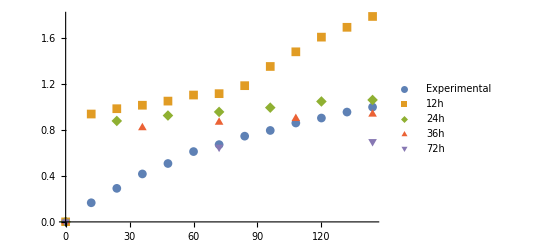

```mathematica
ListPlot[{RealLutA,CROSSLUT1[[1]],CROSSLUT1[[2]],CROSSLUT1[[3]],CROSSLUT1[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

```mathematica
(*Type 1, 1 Layer, lower training/repetition of datasets*)
```

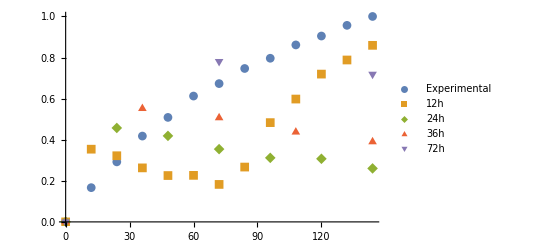

```mathematica
ListPlot[{RealLutA,CROSSLUT2[[1]],CROSSLUT2[[2]],CROSSLUT2[[3]],CROSSLUT2[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

```mathematica
(*Type 1, 2 Layers*)
```

```mathematica
ListPlot[{RealLutA,CROSSLUT3[[1]],CROSSLUT3[[2]],CROSSLUT3[[3]],CROSSLUT3[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

-Graphics-

```mathematica
(*Type 1, 2 Layer, lower training/repetition of datasets*)
```

```mathematica
ListPlot[{RealLutA,CROSSLUT4[[1]],CROSSLUT4[[2]],CROSSLUT4[[3]],CROSSLUT4[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

-Graphics-

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

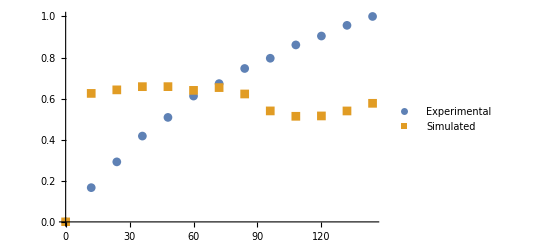

```mathematica
ListPlot[{RealLutA,CROSSLUT5},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

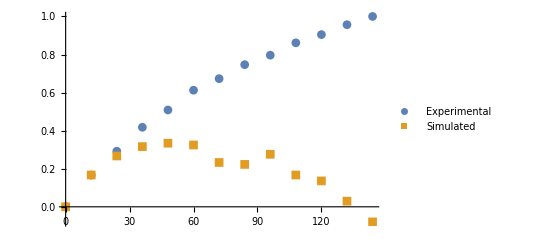

```mathematica
ListPlot[{RealLutA,CROSSLUT6},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

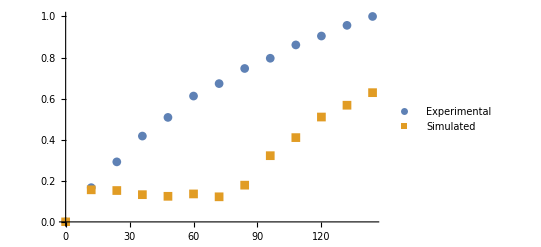

```mathematica
ListPlot[{RealLutA,CROSSLUT7},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

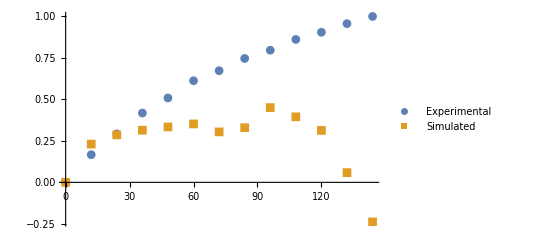

```mathematica
ListPlot[{RealLutA,CROSSLUT8},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

### Nit

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
legendLab={"Experimental","12h","24h","36h","72h"}
```

{Experimental,12h,24h,36h,72h}

```mathematica
(*Type 1, 1 Layer*)
```

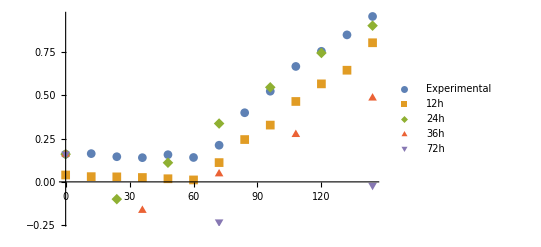

```mathematica
ListPlot[{RealNitA,CROSSNIT1[[1]],CROSSNIT1[[2]],CROSSNIT1[[3]],CROSSNIT1[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

```mathematica
(*Type 1, 1 Layer, lower training/repetition of datasets*)
```

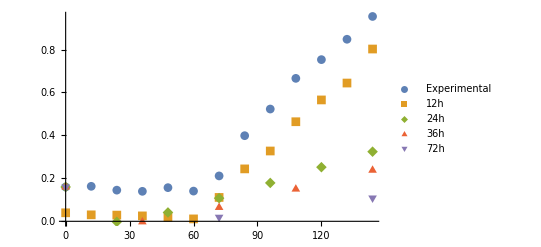

```mathematica
ListPlot[{RealNitA,CROSSNIT2[[1]],CROSSNIT2[[2]],CROSSNIT2[[3]],CROSSNIT2[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

```mathematica
(*Type 1, 2 Layers*)
```

```mathematica
ListPlot[{RealNitA,CROSSNIT3[[1]],CROSSNIT3[[2]],CROSSNIT3[[3]],CROSSNIT3[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

-Graphics-

```mathematica
(*Type 1, 2 Layer, lower training/repetition of datasets*)
```

```mathematica
ListPlot[{RealNitA,CROSSNIT4[[1]],CROSSNIT4[[2]],CROSSNIT4[[3]],CROSSNIT4[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

-Graphics-

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

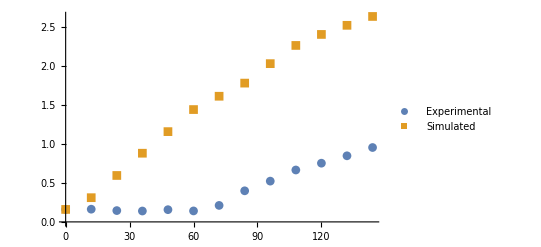

```mathematica
ListPlot[{RealNitA,CROSSNIT5},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

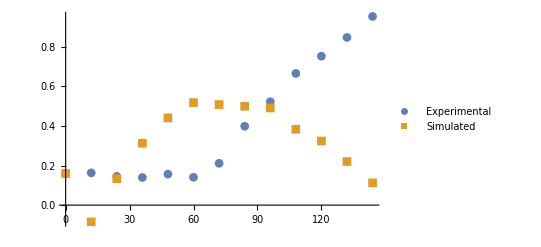

```mathematica
ListPlot[{RealNitA,CROSSNIT6},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

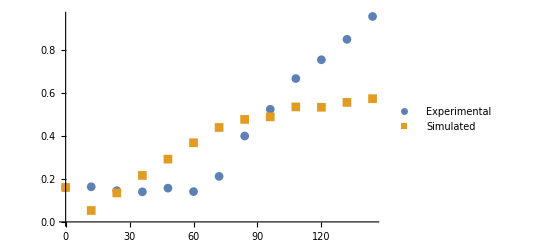

```mathematica
ListPlot[{RealNitA,CROSSNIT7},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

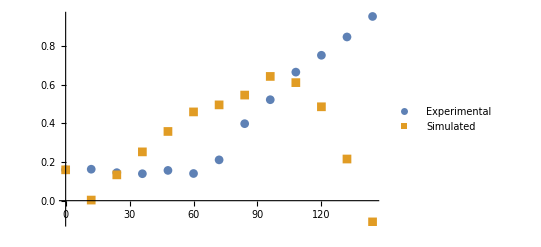

```mathematica
ListPlot[{RealNitA,CROSSNIT8},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

### DCW

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
legendLab={"Experimental","12h","24h","36h","72h"}
```

{Experimental,12h,24h,36h,72h}

```mathematica
(*Type 1, 1 Layer*)
```

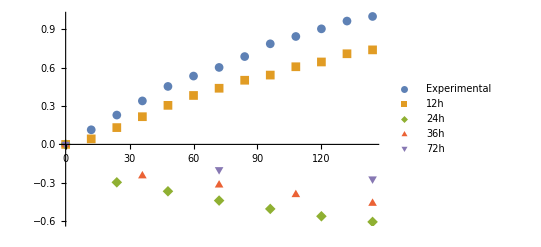

```mathematica
ListPlot[{RealDCWA,CROSSDCW1[[1]],CROSSDCW1[[2]],CROSSDCW1[[3]],CROSSDCW1[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

```mathematica
(*Type 1, 1 Layer, lower training/repetition of datasets*)
```

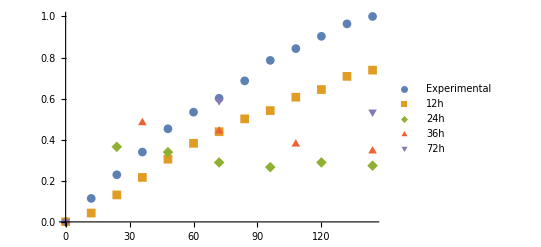

```mathematica
ListPlot[{RealDCWA,CROSSDCW2[[1]],CROSSDCW2[[2]],CROSSDCW2[[3]],CROSSDCW2[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

```mathematica
(*Type 1, 2 Layers*)
```

```mathematica
ListPlot[{RealDCWA,CROSSDCW3[[1]],CROSSDCW3[[2]],CROSSDCW3[[3]],CROSSDCW3[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

-Graphics-

```mathematica
(*Type 1, 2 Layer, lower training/repetition of datasets*)
```

```mathematica
ListPlot[{RealDCWA,CROSSDCW4[[1]],CROSSDCW4[[2]],CROSSDCW4[[3]],CROSSDCW4[[4]]},PlotMarkers->Automatic,PlotLegends->legendLab]
```

-Graphics-

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

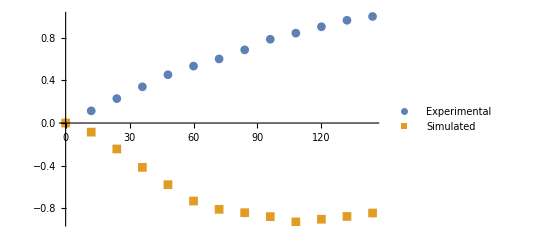

```mathematica
ListPlot[{RealDCWA,CROSSDCW5},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

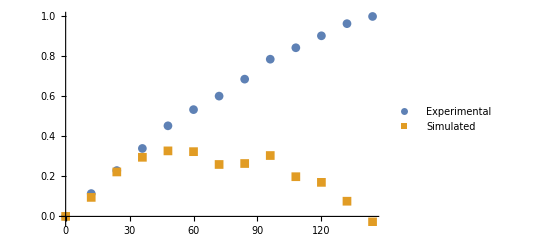

```mathematica
ListPlot[{RealDCWA,CROSSDCW6},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

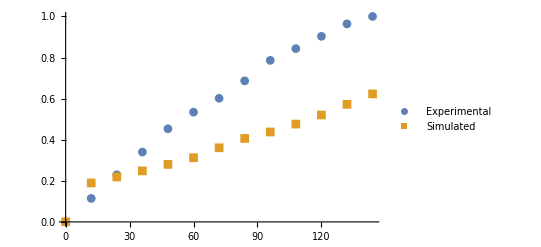

```mathematica
ListPlot[{RealDCWA,CROSSDCW7},PlotMarkers->Automatic,PlotLegends->legendLab2]
```

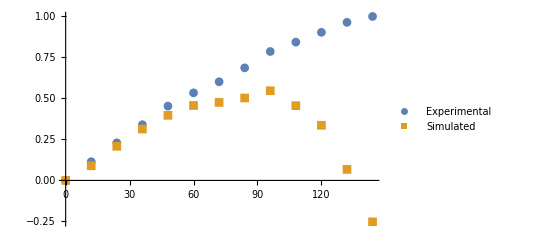

```mathematica
ListPlot[{RealDCWA,CROSSDCW8},PlotMarkers->Automatic,PlotLegends->legendLab2]
```